The geodesic equations are given below (taken from Diff. Geo. of Curves and Surfaces shamelessly):

(ⅆ^2 x^i)/(ⅆ s^2)+∑_(j,k=1)^2 (Γ^i)_jk(ⅆ x^j)/ⅆs(ⅆ x^k)/ⅆs=0   for i = 1,2

where the Christoffel symbols are the (Γ^i)_jk, which characterize the metric on the surface in question. These equations are useful for our purposes because they hold for geodesics parameterized by arc length. These are second order ordinary differential equations, so they require boundary conditions. Since there are two coordinates (x^1,x^2), we must have four boundary conditions (which we will simplify to three by assuming the first derivative has unit magnitude):

x(0)=(x^1(0),x^2(0))
x'(0)=(cosθ u,sinθ v)

where u,v are the unit coordinate vectors at x(0).
For now, let’s skip the difficult part of determining the geodesic parameterization in terms of arc length (either analytically or numerically) and let’s assume that we have found a parameterization for a geodesic on our coordinate map that satisfies the above equations. Since this parameterization is parameterized by arc length, we simply ‘step’ along this geodesic for one step length h:

p_(n+1)=x(h)

where x is the geodesic with x(0)=p_n

This procedure allows us to define a step length h and a random direction θ for each step in our random walk (and thus perform a random walk on any surface that we can solve the geodesic equations for)

### Plane

The Christoffel symbols are identically zero for the entire plane. This leads rather quickly to the analytical solution for geodesics of the familiar line:

x(s)=p_0+u(θ)s

where p_0 is the starting point and θ is an angle from an x-axis. Thus we have the stepping function

p_(n+1)=p_n+u(θ)h

```mathematica
planewalk[steplength_,numsteps_]:=Module[{stepfunc},
stepfunc[{x_,y_}]:=Module[{θ},
θ=RandomReal[{0,2π}];
{x+steplength*Cos[θ],y+steplength*Sin[θ]}
];
NestList[
stepfunc,
{0,0},
numsteps
]];
planehist[steplength_,numsteps_][numpts_]:=Module[{data},
data=Table[Norm[planewalk[steplength,numsteps][[-1]]],{numpts}];
Histogram[{data}]
];
```

From here on, it will be easier to develop code for a more general 2D manifold and apply it to different manifolds with different coordinate maps. (Most of this code and equations are taken from [Geodesics Using Mathematica by Lewis]. The equations we will use are

u'=p
v'=q
p'=-1/(x_u·x_u)(x_uu·x_u p^2+2x_uv·x_up q+x_vv·x_u q^2)
q'=-1/(x_v·x_v)(x_uu·x_v p^2+2x_uv·x_vp q+x_vv·x_v q^2)

where x is the coordinate map from the u-v plane onto the 2D manifold. These equations are a system of four first order ordinary differential equations. We use a similar procedure used as in [Lewis] to translate this system of equations to Mathematica:

```mathematica
Clear[geodesicequations,nsteponce,nsteponceRANDANG];
geodesicequations[{x_,{umin_,umax_},{vmin_,vmax_}}][u_,v_,p_,q_]:=Module[{xu,xv,xuu,xuv,xvv},
xu=D[x[u,v],u];
xv=D[x[u,v],v];
xuu=D[xu,u];
xuv=D[xu,v];
xvv=D[xv,v];
Simplify[
{(-1/xu.xu)*(xuu.xu p^2+2xuv.xu p q+xvv.xu q^2),
(-1/xv.xv)*(xuu.xv p^2+2xuv.xv p q+xvv.xv q^2),
{umin,umax},
{vmin,vmax}}
]
];
nsteponce[geoeqn_,θ_,steplength_][{u0_:0,v0_:0}]:=Module[{urange,vrange,uu,vv,u,v},
urange=geoeqn[u,v,uu,vv][[3]];
vrange=geoeqn[u,v,uu,vv][[4]];
{uu,vv}=NDSolveValue[ 
{u''[s]==geoeqn[u[s],v[s],u'[s],v'[s]][[1]],
v''[s]==geoeqn[u[s],v[s],u'[s],v'[s]][[2]],
u[0]==u0,v[0]==v0,
u'[0]==Cos[θ],v'[0]==Sin[θ]},
{u,v},
{s,0,steplength}];
{urange[[1]]+Mod[uu[steplength],(urange[[2]]-urange[[1]])],
vrange[[1]]+Mod[vv[steplength],(vrange[[2]]-vrange[[1]])]} (* Mod is required to stay within the domain of the coordinate map *)
];
nsteponceRANDANG[geoeqn_,steplength_][{u0_:0,v0_:0}]:=Module[{ang},
ang=RandomReal[{0,2π}];
nsteponce[geoeqn,ang,steplength][{u0,v0}]
];
```

```mathematica
stepcheck[geoeqn_,steplength_,escaperegion_][{{u0_,v0_},t_,prev_}]:=Module[{nextpt,escaped},
nextpt=nsteponceRANDANG[geoeqn,steplength][{u0,v0}];
escaped=TrueQ[nextpt∈escaperegion];
{nextpt,t+1,escaped}
];
```

```mathematica
Module[{sphere,spheremap,geosphere,escapereg,uu,vv,eplot,next},
sphere[u_,v_]:={Cos[u]Cos[v],Cos[v]Sin[u],Sin[v]};
spheremap={sphere,{0,2π},{0,π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
escapereg=ParametricRegion[{uu,vv},{{uu,0,π/2},{vv,0,π/2}}];
eplot=RegionPlot[escapereg,PlotRange->{{0,2π},{0,π}}];
next=stepcheck[geosphere,π/10,escapereg][{{π/4,π/4},0,False}];
next
]
```

{{0.718573,1.09566},1,True}

### Plane

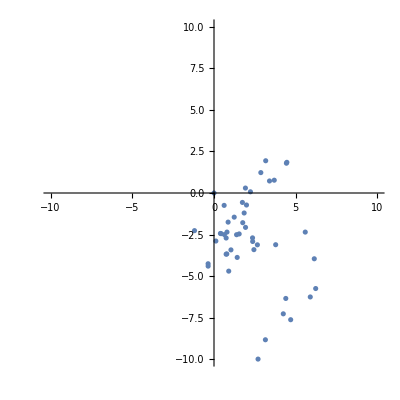

```mathematica
Module[{plane,planemap,geoplane,walk},
plane[u_,v_]:={u,v};
planemap={plane,{-100,100},{-100,100}};
geoplane[u_,v_,p_,q_]=geodesicequations[planemap][u,v,p,q];
walk=NestList[
nsteponceRANDANG[geoplane,1],
{0,0},
100];
ListPlot[walk,PlotRange->{{-10,10},{-10,10}}, AspectRatio->1]
]
```

### Sphere

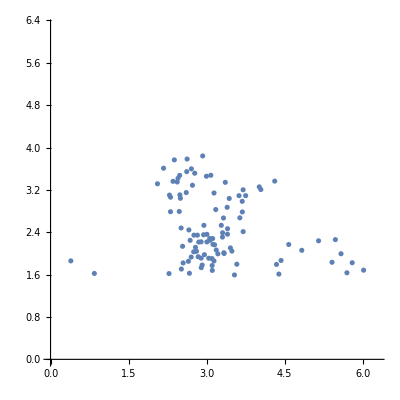

```mathematica
Module[{sphere,spheremap,geosphere,walk},
sphere[u_,v_]:={Cos[u]Cos[v],Cos[v]Sin[u],Sin[v]};
spheremap={sphere,{0,2π},{0,2π}};
geosphere[u_,v_,p_,q_]=geodesicequations[spheremap][u,v,p,q];
walk=NestList[
nsteponceRANDANG[geosphere,π/10],
{π,π},
100];
ListPlot[walk,PlotRange->{{0,2π},{0,2π}},AspectRatio->1]
]
```

### Torus

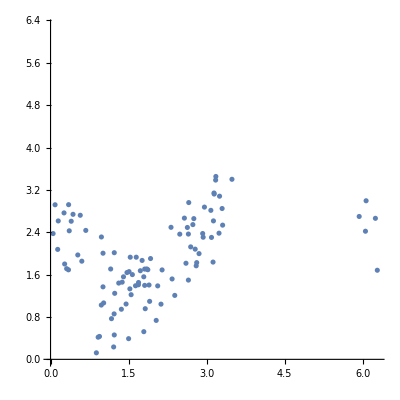

```mathematica
Module[{torus,torusmap,geotorus,walk},
torus[R_,r_][u_,v_]:={(R+r Cos[u])Cos[v],(R+r Cos[u])Sin[v],r Sin[u]};
(*R distance from center of tube to center of torus, r radius of tube, u,v∈[0,2π)*)
torusmap={torus[2,1],{0,2π},{0,2π}};
geotorus[u_,v_,p_,q_]=geodesicequations[torusmap][u,v,p,q];
walk=NestList[
nsteponceRANDANG[geotorus,π/10],
{π,π},
100];
ListPlot[walk,PlotRange->{{0,2π},{0,2π}},AspectRatio->1]
]
```